# Time dilation

-Graphics-

d t'=t'_2−t'_1=γ(t_2−v/c^2 x_2)−γ(t_1−v/c^2 x_1)=γ(t_2−t_1)_dt−γ v/c^2(x_2−x_1)_(v t_2−v t_1)

=γdt−γ(v^2/c)_(β^2)(t_2−t_1)_dt=γdt−γ β^2 dt=γdt(1−β^2)=1/γ dt

⇒dt=γd t'

## Example

### Speed of light

```mathematica
c=299792458;
```

### Relative velocity between inertial reference frames

```mathematica
v=0.8c;
```

### Ratio of relative velocity v to the speed of light c

```mathematica
β[𝓋_]=𝓋/c;
```

### Lorentz factor

```mathematica
γ[𝓋_]=1/(√(1-β[𝓋]^2));
```

### Proper time

Le temps propre d’un objet en mouvement est simplement le temps tel qu’il s’écoule dans le référentiel de l’objet.

```mathematica
dt':=1
```

### Time

```mathematica
dt[𝓋_]=γ[𝓋]dt';
```

```mathematica
dt[v]
```

1.66667

## Plot

```mathematica
Plot1=Plot[dt[𝓋],{𝓋,0,c},FrameLabel->{"v (m/s)","dt (m)"},PlotLegends->"Expressions",Frame-> True,GridLines->Automatic];
```

```mathematica
Plot2=ListPlot[{{v,dt[v]}},MeshStyle->Red,PlotMarkers->{Automatic,Medium}];
```

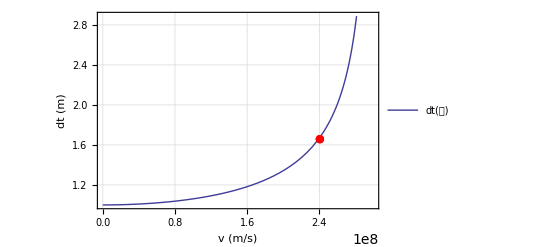

```mathematica
Show[Plot1,Plot2]
```